```mathematica
ClearAll["`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Once[Get["Project2.m","IX1501"]]
```

```mathematica
n = 50;
```

```mathematica
randomSample = randomNumber[0,n];
```

```mathematica
sort = Sort[randomSample]
```

{0.664625,2.08814,2.13878,2.15284,2.26393,2.43268,2.50534,2.6408,2.73694,2.94327,3.10208,3.21918,3.45622,3.88569,4.27648,4.32943,4.4705,4.62006,4.75824,4.88378,5.01067,5.1786,5.24871,5.25531,5.27217,5.27654,5.33688,5.54047,5.98285,6.12811,6.22733,6.45861,6.46217,6.57159,6.60451,6.82074,6.99984,7.18013,7.25275,7.44654,7.46834,7.54001,7.85851,8.2691,8.79332,9.07355,9.20322,10.2036,12.1211,12.847}

```mathematica
Δ=1/n;
pdata=Δ/2+Range[0,1-Δ,Δ]//N;
```

```mathematica
cdf = Transpose[{sort, pdata}];
```

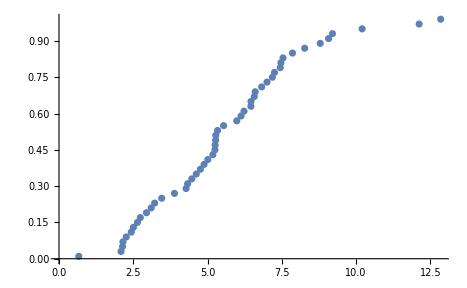

```mathematica
ListPlot[cdf]
```

```mathematica
μ = Mean[sort]
```

5.58402

```mathematica
s = StandardDeviation[sort]
```

2.59478

```mathematica
solA = NSolve[Integrate[x*E^(-a*x), {x, 0, ∞}] == μ, a][[1]][[1]][[2]]
```

0.423181

```mathematica
solA
```

0.423181

```mathematica
solA2 =NSolve[Integrate[x*x*E^(-a*x), {x, 0, ∞}] == μ, a, Reals][[1]][[1]][[2]]
```

0.710168

```mathematica
pdf1[x_] := E^(-solA*x)
```

```mathematica
pdf2[x_] = x*E^(-solA2*x)
```

ⅇ^(-0.710168 x) x

```mathematica
pdf3[x_] := x*(x+0)*E^(-0*x)
```

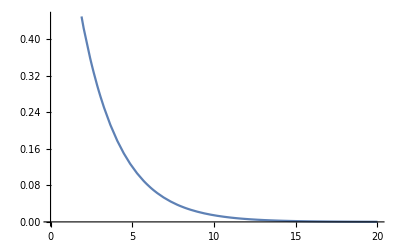

```mathematica
Show[Plot[pdf1[x], {x, 0, 20}]]
```

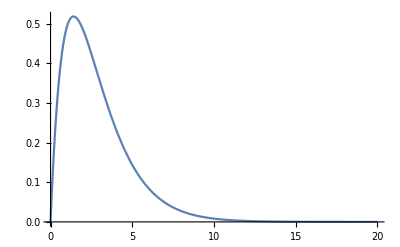

```mathematica
Plot[pdf2[x], {x, 0, 20}]
```

```mathematica
(*NSolve[{Integrate[x^2 * x*(x+b)*E^(-a*x) - (x*x*(x+b)*E^(-a*x))^2, {x, 0, n}]== s^2, Integrate[(x+b)*x*x*E^(-a*x), {x, 0, n}] == μ}, {a,b}]*)
```

```mathematica
listFun1[x_] := pdf1[sort[[x]]]
```

```mathematica
modelList1 = Array[listFun1, n];
```

```mathematica
comparedata1 = Transpose[{modelList1,pdata}];
```

```mathematica
dataplot1=ListPlot[comparedata1,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"comparing cdf", PlotRange->{0, 1}];
```

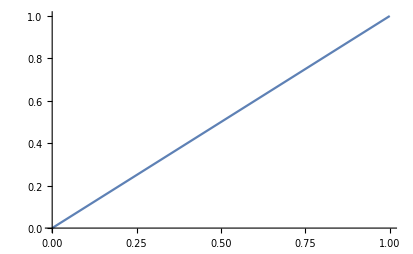

```mathematica
lineplot =Plot[x, {x, 0, 1}]
```

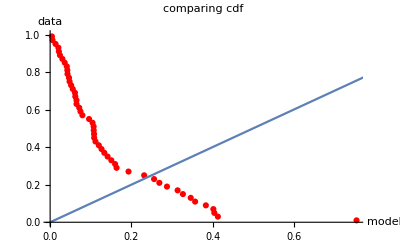

```mathematica
Show[dataplot1,lineplot]
```

```mathematica
listFun2[x_] := pdf2[sort[[x]]]
```

```mathematica
modelList2= Array[listFun2, n];
```

```mathematica
comparedata2 = Transpose[{modelList2,pdata}];
```

```mathematica
dataplot2=ListPlot[comparedata2,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"comparing cdf", PlotRange->{0, 1}];
```

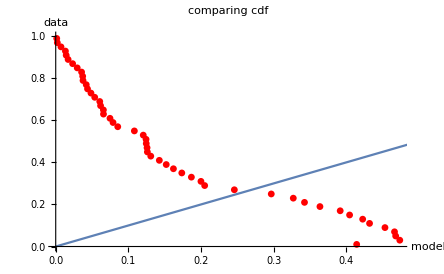

```mathematica
Show[dataplot2,lineplot]
```

```mathematica
ClearAll["`*"]
```

```mathematica
n = 1000;
```

```mathematica
m = 10000;
```

First distribution------------------------------------------------------------------------------------------

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Once[Get["Project2.m","IX1501"]]
```

```mathematica
Needs["HypothesisTesting`"]
```

```mathematica
numbers = randomNumber[1, n];
FindDistribution[numbers]
```

ExponentialDistribution[4.27876]

```mathematica
Δ=1/n;
pdata=Δ/2+Range[0,1-Δ,Δ]//N;
```

```mathematica
sort = Sort[numbers];
```

```mathematica
μ = Mean[numbers]
```

0.233712

```mathematica
distribution = ExponentialDistribution[1/μ];
```

```mathematica
cdf = CDF[distribution, sort];
```

```mathematica
comparedata = Transpose[{cdf, pdata}];
```

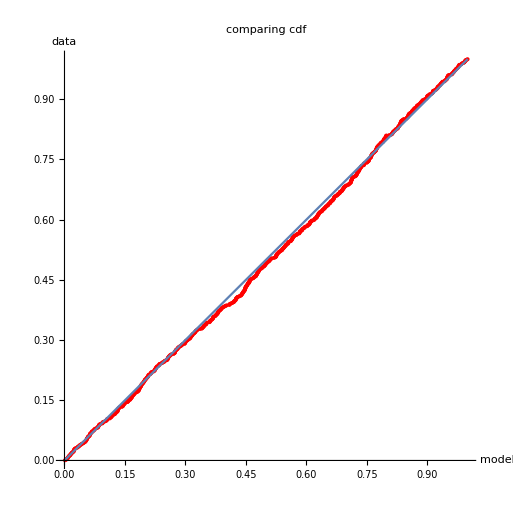

```mathematica
dataplot=ListPlot[comparedata,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"comparing cdf",AspectRatio->Automatic];
lineplot=Plot[x,{x,0,1}];
Show[dataplot,lineplot]
```

```mathematica
𝕩=randomNumber[1,{n,m}];
```

```mathematica
findlambda[data_]:=List@@EstimatedDistribution[data,ExponentialDistribution[λ]]
```

```mathematica
lambda=Transpose[findlambda/@𝕩][[1]];
```

```mathematica
cilambda=MeanCI[lambda, ConfidenceLevel->0.95]
```

{4.48527,4.49081}

Andra saken -------------------------------------------------------------------------------------

```mathematica
ClearAll["`*"]
```

```mathematica
n = 10000;
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Once[Get["Project2.m","IX1501"]]
```

```mathematica
numbers = randomNumber[2, n];
distribution= FindDistribution[numbers]
```

GeometricDistribution[0.0651037]

```mathematica
Δ=1/n;
pdata=Δ/2+Range[0,1-Δ,Δ]//N;
```

```mathematica
sort = Sort[numbers];
```

```mathematica
cdf = CDF[distribution, sort];
```

```mathematica
comparedata = Transpose[{cdf, pdata}];
```

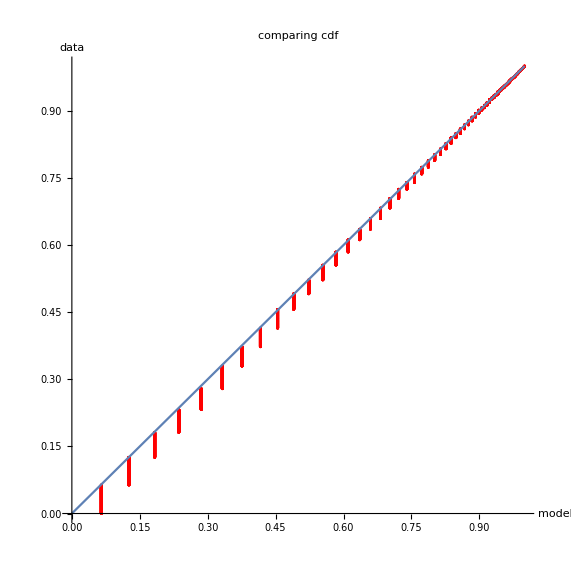

```mathematica
dataplot=ListPlot[comparedata,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"comparing cdf",AspectRatio->Automatic];
lineplot=Plot[x,{x,0,1}];
Show[dataplot,lineplot]
```

```mathematica
Clear [𝕩,p]
```

```mathematica
Needs["HypothesisTesting`"]
```

```mathematica
n=100;
m=1000;
𝕩=randomNumber[2,{n,m}];
```

```mathematica
List
```

List

```mathematica
findprob[data_]:=List@@EstimatedDistribution[data,GeometricDistribution[p]]
```

```mathematica
prob=Transpose[findprob/@𝕩][[1]];
```

```mathematica
ciprob=MeanCI[prob, ConfidenceLevel->0.95]
```

{0.0645201,0.065361}

```mathematica
ciprob[[2]]/ciprob[[1]]
```

1.01303

Tredje saken -------------------------------------------------------------------------------------

```mathematica
ClearAll["`*"]
```

```mathematica
n = 1000;
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Once[Get["Project2.m","IX1501"]]
```

```mathematica
numbers = randomNumber[3, n];
FindDistribution[numbers]
```

GammaDistribution[7.83815,1.59817]

```mathematica
distribution=EstimatedDistribution[numbers,GammaDistribution[α,β]]
```

GammaDistribution[7.931,1.59694]

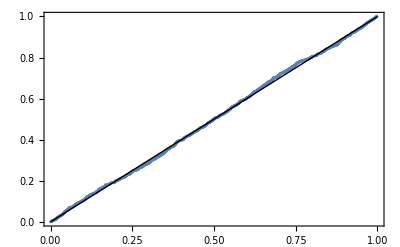

```mathematica
ProbabilityPlot[numbers, distribution]
```

```mathematica
Clear[𝕩, p, α,β, 𝕒,𝕓]
```

```mathematica
Needs["HypothesisTesting`"]
```

```mathematica
n=100;
m=1000;
𝕩=randomNumber[3,{n,m}];
```

```mathematica
findαβ[data_]:=List@@EstimatedDistribution[data,GammaDistribution[α,β]]
```

```mathematica
{𝕒,𝕓}=Transpose[findαβ/@𝕩];
```

```mathematica
ciα=MeanCI[𝕒, ConfidenceLevel->0.95]
```

{8.0109,8.15679}

```mathematica
ciβ=MeanCI[𝕓, ConfidenceLevel->0.95]
```

{1.57503,1.60395}

```mathematica
ciα[[2]]/ciα[[1]]
```

1.01821

Fjärde saken -------------------------------------------------------------------------------------

```mathematica
ClearAll["`*"]
```

```mathematica
n = 1000;
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Once[Get["Project2.m","IX1501"]]
```

```mathematica
numbers = randomNumber[4, n];
FindDistribution[numbers]
```

NormalDistribution[3.02424,5.20237]

```mathematica
μ = Mean[numbers];
```

```mathematica
σ = StandardDeviation[numbers];
```

```mathematica
distribution=EstimatedDistribution[numbers, NormalDistribution[μ,σ]]
```

NormalDistribution[3.02424,5.20497]

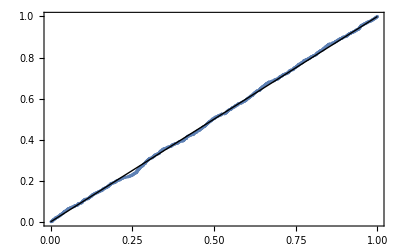

```mathematica
ProbabilityPlot[numbers, distribution]
```

```mathematica
Clear[𝕩,p,σ ,μ,𝕒,𝕓]
```

```mathematica
Needs["HypothesisTesting`"]
n=100;
m=1000
𝕩=randomNumber[4,{n,m}];
```

1000

```mathematica
findNorm[data_]:=List@@EstimatedDistribution[data,NormalDistribution[σ ,μ]]
```

```mathematica
{𝕒,𝕓}=Transpose[findNorm/@𝕩];
```

```mathematica
ciσN=MeanCI[𝕒, ConfidenceLevel->0.95]
```

{2.99481,3.05382}

```mathematica
ciμN=MeanCI[𝕓, ConfidenceLevel->0.95]
```

{4.96676,5.01253}

```mathematica
ciσN[[2]]/ciσN[[1]]
```

1.01971

```mathematica
ciμN[[2]]/ciμN[[1]]
```

1.00921

Femte saken -------------------------------------------------------------------------------------

```mathematica
ClearAll["`*"]
```

```mathematica
n = 1000;
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Once[Get["Project2.m","IX1501"]]
```

```mathematica
numbers = randomNumber[5, n];
FindDistribution[numbers]
```

BinomialDistribution[14,0.234626]

```mathematica
distribution = EstimatedDistribution[numbers, BinomialDistribution[n, p]]
```

BinomialDistribution[1000,0.003277]

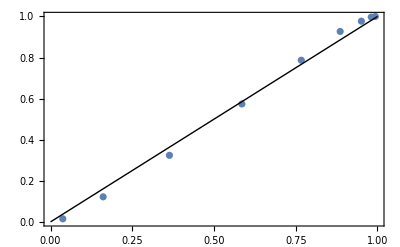

```mathematica
ProbabilityPlot[numbers, distribution]
```

```mathematica
Clear[𝕩,p,𝕒]
```

```mathematica
Needs["HypothesisTesting`"]
```

```mathematica
n=100;
m=1000;
𝕩=randomNumber[5,{n,m}];
```

```mathematica
findBin[data_]:=List@@EstimatedDistribution[data,BinomialDistribution[m ,p]]
```

```mathematica
binom=Transpose[findBin/@𝕩][[2]];
```

```mathematica
cibin=MeanCI[binom, ConfidenceLevel->0.95]
```

{0.00328118,0.00329928}

```mathematica
(cibin[[2]]/cibin[[1]])
```

1.00552

Sjätte saken -------------------------------------------------------------------------------------

```mathematica
ClearAll["`*"]
```

```mathematica
n = 1000;
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Once[Get["Project2.m","IX1501"]]
```

```mathematica
numbers = randomNumber[6, n];
FindDistribution[numbers]
```

PoissonDistribution[9.905]

```mathematica
μ=Mean[numbers];
```

```mathematica
distribution = EstimatedDistribution[numbers, PoissonDistribution[μ]];
```

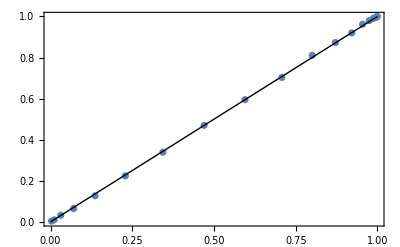

```mathematica
ProbabilityPlot[numbers, distribution]
```

```mathematica
Clear[𝕩,μ]
```

```mathematica
Needs["HypothesisTesting`"]
```

```mathematica
n=100;
m=1000;
𝕩=randomNumber[6,{n,m}];
```

```mathematica
findpoiss[data_]:=List@@EstimatedDistribution[data,PoissonDistribution[μ]]
```

```mathematica
poisson=Transpose[findpoiss/@𝕩][[1]];
```

```mathematica
cipoiss=MeanCI[poisson, ConfidenceLevel->0.95]
```

{9.78433,9.82139}

```mathematica
(cipoiss⟦2⟧/cipoiss⟦1⟧)
```

1.00379